```mathematica
(* 
1 - коллокация в точке;
2 - коллокация в подобластях;
3 - метод Бубнова - Галеркина;
4 - метод Галеркина;
5 - МНК; 
6 - метод Ритца;
*)
methodNumber =6; (* номер метода *)
p = 2; (* порядок *)
```

```mathematica
(* Дано *)
leftSide=0;
rightSide=1;
A[phi_,x_]:=D[phi,{x,2}]+phi;
F[x_]:=-x;
phiI[x_,i_]:=x^i-x^(i+1);
```

```mathematica
(* Решение *)
projectionMethod[methodNumber_,order_]:=Module[{a,u,psi,leftEquation,eqRight,aValue,numericalSolution},
a=Table[Subscript[aa, i],{i,1,order}];

Switch[methodNumber,
1,psi=Table[DiracDelta[x-(leftSide + i (rightSide-leftSide)/(order+1))],{i,1,order}],
2,psi=Table[If[leftSide+(i-1)(rightSide-leftSide)/order≤x<leftSide+i(rightSide-leftSide)/order,1,0],{i,1,order}],
3,psi=Table[phiI[x,i],{i,1,order}],
4,psi=Table[(x-1/2)^(i-1),{i,1,order}],
5,psi=Table[A[phiI[x,i],x],{i,1,order}],
6,
u=Dot[a,Table[phiI[x,i],{i,1,order}]];
psi=Table[D[u,Subscript[aa, i]],{i,1,order}]
];
leftEquation=Table[Sum[a⟦i⟧Integrate[A[phiI[x,i],x]psi⟦j⟧, {x, leftSide, rightSide}],{i, 1, order}],{j,1,order}];
eqRight=Table[Integrate[F[x]psi⟦j⟧, {x, leftSide, rightSide}],{j,1,order}];
aValue=Solve[leftEquation==eqRight,a];
numericalSolution[x_]:=Sum[a⟦i⟧phiI[x,i], {i, 1, order}]/.aValue;
Return[{a/.aValue,numericalSolution[x]}];
]
```

```mathematica
getResults[methodNumber_,order_]:=Module[{analyticalSolution,i,a,numericalSolution,deltha,tableFraction,tableNum,tableErr,plot},
analyticalSolution[x]:=DSolve[{A[u[xi],xi]==F[xi],u[leftSide]==0,u[rightSide]==0},u[xi],xi]⟦1,1,2⟧/.xi->x;
result={};
For[i=1,i≤order,i++,
{a,numericalSolution[x]}=projectionMethod[methodNumber,i];
deltha=N@Sqrt[(Integrate[(analyticalSolution[x]-numericalSolution[x])^2,{x,leftSide,rightSide}]/Integrate[(analyticalSolution[x])^2,{x,leftSide,rightSide}])];
AppendTo[result,{a,numericalSolution[x],deltha}];
];
plotDataSolutions=result⟦1;;Min[3,Length[result]],2⟧;
AppendTo[plotDataSolutions,analyticalSolution[x]];
tableFraction = Grid[Prepend[Transpose@{Table[i,{i,1,order}],result⟦;;,1⟧},{"n","a_i, fraction"}],Frame->All];
tableNum =Grid[Prepend[Transpose@{Table[i,{i,1,order}],N@result⟦;;,1⟧},{"n","a_i, decimal"}],Frame->All];
tableErr=Grid[Prepend[Transpose@{Table[i,{i,1,order}],result⟦;;,3⟧},{"n","deltha"}],Frame->All];
plot=Plot[plotDataSolutions,{x,leftSide,rightSide},PlotLegends->Append[Table["numerical, p = "<>ToString[i],{i,1,Min[order,3]}],"analytical"],AxesStyle->Black,LabelStyle->{13,Black},AxesLabel->{"x","u(x)"},PlotRange->All, ImageSize->700, PlotStyle->{Purple, Blue, Green, {Gray, Dashed}}];
Return[{tableFraction, tableNum, tableErr, plot}];
]
```

```mathematica
(* Результаты *)
results = getResults[methodNumber,p];
```

```mathematica
(* коэффициенты приближенного решения в виде обыкновенных дробей *)
results[[1]]
```

n | a_i, fraction
1 | {{5/18}}
2 | {{71/369,7/41}}

```mathematica
(* коэффициенты приближенного решения в виде десятичных дробей *)
results[[2]]
```

n | a_i, decimal
1 | {{0.277778}}
2 | {{0.192412,0.170732}}

```mathematica
(* относительная ошибка *)
results[[3]]
```

n | deltha
1 | {0.115426}
2 | {0.00371191}

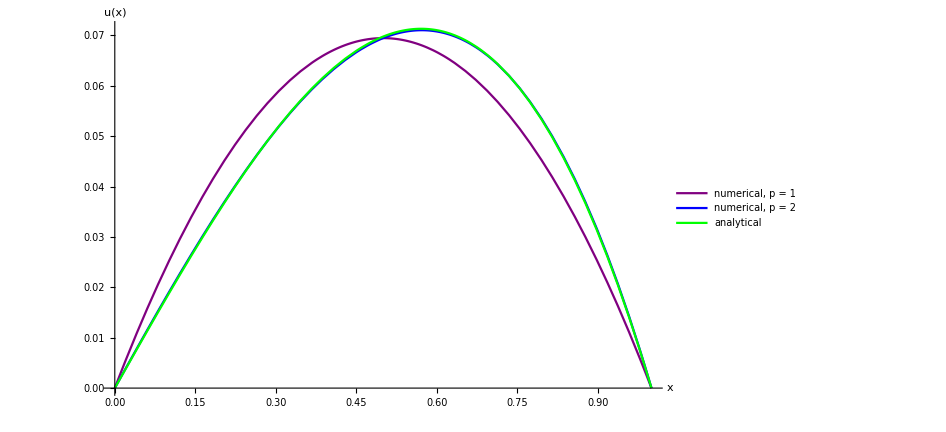

```mathematica
(* графики точного и численного решения *)
results[[4]]
```